```mathematica
SetDirectory[NotebookDirectory[]]
```

/work/qd-engine

## Quantum dynamics analyst

### Basic constants

```mathematica
c=(Entity["PhysicalConstant","SpeedOfLight"]["Value"]//QuantityMagnitude)*100;(* Speed of light in cm/s *)
```

### Import data:

```mathematica
posCF=Import["corrF.dat","Table"][[2;;]];
dt=posCF[[1,1]];
ampData = Import["PAmp.dat","Table"][[2;;]];
xSpace=ampData[[1]];
potential=Import["test/potential.dat","Table"];
```

### Functions:

```mathematica
GetSpectrum[cf_List,dt_]:=
	Module[{signal,spectrum, wns, wnMax},
		signal=cf-Mean[cf];
		signal=Join[signal,ConstantArray[0,Length[signal]*10]];
		wns=Table[1/(Length[signal]*dt*1*^-15)/c*i,{i,0,Length[signal]-1}];
		spectrum = Abs[Fourier[signal]]^2;
		wnMax=Round[Length[signal]*dt*1*^-15*c*4500];
		Return[Transpose[{wns,spectrum}][[;;wnMax]]]
];

PlotSpectrum[data_List,xRange_List,label_String]:=
	Labeled[
	ListLinePlot[data,
		PlotRange->{xRange,All},
		Frame->True,
		FrameStyle->Directive[Black,14,FontFamily->"Helvetica",AbsoluteThickness[1.2]],
		ImageSize->250,
		GridLines->Automatic],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{"Intensity","Wavenumber [cm^-1]",label},
{Left,Bottom,Top},RotateLabel->True]
PlotAmp[i_Integer]:=Module[{pltPot,pltAmp},
	pltPot=ListLinePlot[potential,
		PlotRange->{{-.25,.45},{0,.03}},
		Frame->True,
		Axes->False,
		FrameStyle->Directive[12,Black,AbsoluteThickness[1.2],FontFamily->"Helvetica"],
		GridLines->Automatic,
		PlotStyle->Black];
	pltAmp=ListLinePlot[Transpose[{xSpace,ampData[[i+1,2;;]]/4}],
		PlotRange->All,
		Filling->Axis];
Labeled[
	Show[{pltPot,pltAmp},ImageSize->250,Epilog->{Text[Style["t = "<>ToString@Round@ampData[[i+1,1]]<>" fs",14,FontFamily->"Helvetica"],{.28,.022}]}],
	Style[#,14,FontFamily->"Helvetica"]&/@{"Energy [Hartree]","Distance [Bohr]"},{Left,Bottom},RotateLabel->True]
];
```

### Analyses

#### Probability amplitude evolution

```mathematica
anim=Animate[PlotAmp[i],{i,1,Length[ampData]-1,2},Deployed->True,AnimationRate->100]
```

```mathematica
(*Export["PAmp-anim.mp4",anim,ImageResolution->500]*)
```

#### Position-position autocorrelation function

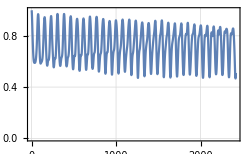
-Graphics-,|⟨ψ(0)|ψ(t)⟩|^2Time [fs]

```mathematica
posCFPlot=Labeled[
	ListLinePlot[posCF[[;;]],
		PlotRange->{All,All},
		Frame->True,
		FrameStyle->Directive[Black,12,FontFamily->"Helvetica",AbsoluteThickness[1.2]],
		ImageSize->250,
		GridLines->Automatic],
Style[#,Black,14,FontFamily->"Helvetica"]&/@{",|⟨ψ(0)|ψ(t)⟩|^2","Time [fs]"},
{Left,Bottom,Top},RotateLabel->True]
```

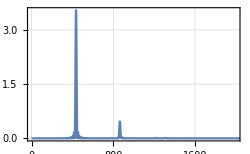
-Graphics-IntensityWavenumber [cm^-1]Position-position spectrum

```mathematica
posSpectrum=GetSpectrum[posCF[[;;,2]],dt];
PlotSpectrum[posSpectrum,{0,2000},"Position-position spectrum"]
```